```mathematica
SetDirectory[NotebookDirectory[]];
Get["funkcije.m"]
```

```mathematica
n = Input["Število naključnih točk n:"];
t0 = tocke[n];
{znotraj,zunaj}=preveri[t0];
```

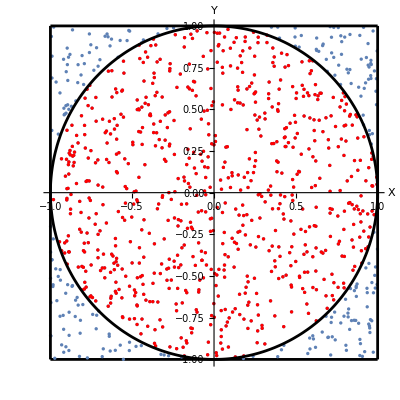

```mathematica
P1=ListPlot[t0,PlotStyle->PointSize[0.006],AxesLabel->{"X","Y"},AspectRatio->1];
P2=ListPlot[znotraj,PlotStyle->{PointSize[0.006],Red},AspectRatio->1];
P3=ParametricPlot[{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->Black,AspectRatio->1];
P4=ParametricPlot[{x,1},{x,-1,1},PlotStyle->Black];
P5=ParametricPlot[{x,-1},{x,-1,1},PlotStyle->Black];
P6=ParametricPlot[{1,x},{x,-1,1},PlotStyle->Black];
P7=ParametricPlot[{-1,x},{x,-1,1},PlotStyle->Black];
Show[P1,P2,P3,P4,P5,P6,P7,AspectRatio->1]
```

```mathematica
{priblizekPi,napaka}=izracunPi[{znotraj,zunaj}];

Print["Približek Pi pri računanju z ",n," točk je ",priblizekPi,".\n","Ta od prave vrednosti odstopa za ",napaka];
```

Približek Pi pri računanju z 1000 točk je 3.04.
Ta od prave vrednosti odstopa za 0.101593

```mathematica
(* izračnu Pi pri 500 -> 20000 točk *)
{priblizkiPi,napake}=calcPi[];
t = Table[{i 500,priblizkiPi[[i]]},{i,1,Length[priblizkiPi]}];
```

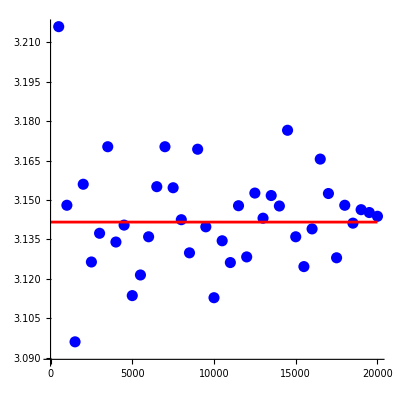

```mathematica
LP1=ListPlot[t,PlotStyle->{PointSize[0.02],Blue},AspectRatio->1];
LP2=ParametricPlot[{x,Pi},{x,0,20000},PlotStyle->Red];
Show[LP1,LP2]
```